I’m not presently using any machinery from “2023-12-04 Plot LPS for L1 L2 phase sweeps v2.nb” but that’ll give nicer results

## Single

```mathematica
raw = Import["~/tmpSLACData/-20_-38.h5","Data"];
Keys[raw]
```

{/momentum/x,/momentum/y,/momentum/z,/position/x,/position/y,/position/z,/time,/weight}

```mathematica
rawToAssoc[raw_]:=(
data=Table[
Association[
{
"x"->raw[["/position/x",i]],
"y"->raw[["/position/y",i]],
"z"->raw[["/position/z",i]],

"px"->raw[["/momentum/x",i]],
"py"->raw[["/momentum/y",i]],
"pz"->raw[["/momentum/z",i]]
}
],
{i,Length[raw[["/momentum/x"]]]}
];
data)
```

```mathematica
data=rawToAssoc[raw];
```

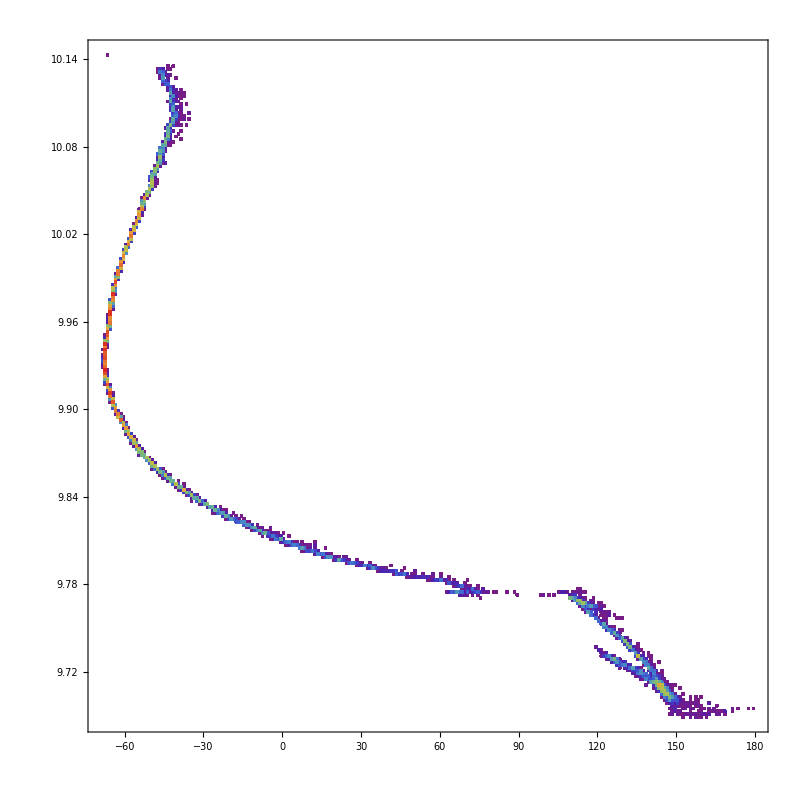

```mathematica
DensityHistogram[
{1*^6 * #z,1*^-9*#pz}&/@data,
{200,200},
ColorFunction->"Rainbow",
LabelStyle->20,
ImageSize->800
]
```

## Automate

```mathematica
fileNames = FileNames["~/tmpSLACData/*_*.h5"];
fileNameToKey[fileName_]:=StringSplit[fileName,{"/",".","_"}][[-3;;-2]]
```

```mathematica
results = Association[
Table[
fileNameToKey[fileName]-> rawToAssoc[Import[fileName,"Data"]],
{fileName,fileNames}
]
];
```

```mathematica
Keys[results]
```

{{-16,-36},{-16,-38},{-16,-40},{-16,-42},{-16,-44},{-16,-46},{-18,-36},{-18,-38},{-18,-40},{-18,-42},{-18,-44},{-18,-46},{-20,-36},{-20,-38},{-20,-40},{-20,-42},{-20,-44},{-20,-46},{-22,-36},{-22,-38},{-22,-40},{-22,-42},{-22,-44},{-22,-46},{-24,-36},{-24,-38},{-24,-40},{-24,-42},{-24,-44},{-24,-46},{-26,-36},{-26,-38},{-26,-40},{-26,-42},{-26,-44},{-26,-46}}

```mathematica
L1Values = DeleteDuplicates[Keys[results][[All,1]]]
L2Values = DeleteDuplicates[Keys[results][[All,2]]]
```

{-16,-18,-20,-22,-24,-26}

{-36,-38,-40,-42,-44,-46}

```mathematica
standardizedPlotting[data_,title_]:=DensityHistogram[
{1*^6 * #z,1*^-9*#pz}&/@data,
{200,200},
ColorFunction->"Rainbow",
LabelStyle->20,
ImageSize->400,
PlotRange->{{-500,500},{9.7,10.2}},
PlotLabel->title
]
```

```mathematica
Dynamic[{L1Set,L2Set}]
imgArr=Table[
standardizedPlotting[results[{L1Set,L2Set}],{L1Set,L2Set}],
{L1Set,L1Values},
{L2Set,L2Values}
];
```

```mathematica
img=GraphicsGrid[imgArr,ImageSize->3200];
```

```mathematica
Export["~/gridConstant.png",img]
```

~/gridConstant.png